```mathematica
ClearAll;
Density=1000.0;
Gravity=9.8;
Zin=1.0;
As=0.04*0.04;
At=1.0;
K=As*Sqrt[2*Gravity]/At
```

0.0070835

```mathematica
Eq1 = Z'[t] == -K*Sqrt[Z[t]]
ZZ[t_]=Z[t]/.First@FullSimplify[DSolve[{Eq1,Z[0]==Zin},Z[t],t]];
```

Z'[t]==-0.0070835 √Z[t]

```mathematica
ZZ[t]
```

1.+(-0.0070835+0.000012544 t) t

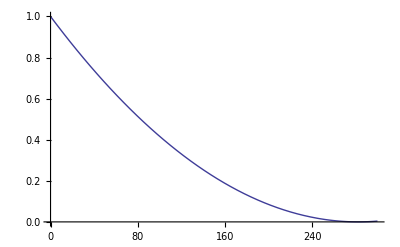

```mathematica
Plot[ZZ[t],{t,0,300}]
```

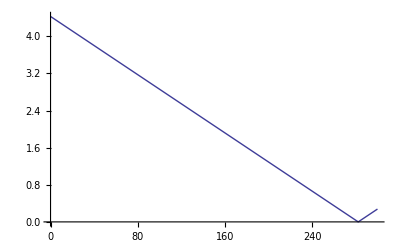

```mathematica
VV[t_] := Sqrt[2*Gravity*ZZ[t]];
Plot[VV[t],{t,0,300}]
```